# First Notebook

## Mathematica Course

James Chryssanthacopoulos

## Section 1

### Subsection 1

This is a subsection

```mathematica
Sin[π]
```

0

```mathematica
D[(1+ x^2), x]
```

2 x

```mathematica
∫Cos[√(x+1)]ⅆx
```

2 Cos[√(1+x)]+2 √(1+x) Sin[√(1+x)]

```mathematica
Series[Exp[x], {x, 0, 10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

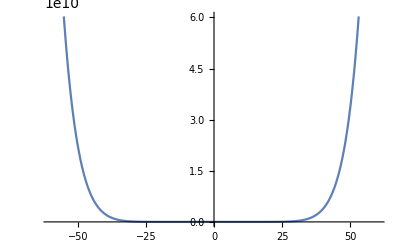

```mathematica
Plot[Evaluate[Normal[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11]],{x,-60.,60.}]
```

```mathematica
Fibonacci[10, x]
```

5 x+20 x^3+21 x^5+8 x^7+x^9

```mathematica
Integrate[x^3/(Exp[x]+1),{x,0,∞}]
```

(7 π^4)/120

```mathematica
∫_0^∞ x^3/(Exp[x]+1)ⅆx
```

(7 π^4)/120

```mathematica
Range[10, 20]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
?Fibonacci
```

```mathematica
??Fibonacci
```

```mathematica
?Plot*
```

```mathematica
x=2
```

2

```mathematica
N[x^2]
```

4.

```mathematica
Pi
```

π

```mathematica
I^2
```

-1

```mathematica
π*2
```

2 π

```mathematica
Π
```

Π

```mathematica
∫yⅆy
```

y^2/2

```mathematica
MatchQ[μ, µ]
```

False

```mathematica
quadratic = ay^2+by+c;
```

```mathematica
quadratic
```

ay^2+by+c

```mathematica
a = b=c=d=π^i
```

π^i

```mathematica
N[a]
```

3.14159^i

```mathematica
b
```

π^i

```mathematica
Clear[a,b,c,d]
```

```mathematica
a
```

a

```mathematica
Clear["Global`*"]
```

```mathematica
x
```

x

```mathematica
ab
```

ab

```mathematica
a/(b∫xⅆx)
```

(2 a)/(b x^2)

```mathematica
a/b
```

a/b

```mathematica
a 4^(1/9)
```

2^(2/9) a

```mathematica
Dot[a,b]
```

a.b

```mathematica
87.3^0.3
```

3.82212

```mathematica
(-2.5)^(1/4)
```

0.88914+0.88914 ⅈ

```mathematica
Sqrt[2]
```

√2

```mathematica
N[(8!)^2/13^9]
```

0.153303

```mathematica
N[π,20]
```

3.1415926535897932385

```mathematica
F[x]=x^2
```

x^2

```mathematica
sin[π/4]
```

sin[π/4]

```mathematica
a = 2(*hello*)
```

2

```mathematica
a=4;
b=2;
c=3;
```

```mathematica
E^π
```

ⅇ^π

```mathematica
1./2
```

0.5

```mathematica
NumberForm[N[e^(2π)],10]
```

e^6.283185307

```mathematica
a=(-2.)^(1/4)
```

0.840896+0.840896 ⅈ

```mathematica
a
```

0.840896+0.840896 ⅈ

```mathematica
a^4
```

-2.+1.25607×10^-15 ⅈ

```mathematica
Chop[a^4]
```

-2.

```mathematica
?AccountingForm
```

```mathematica
Clear[a,b,c,x]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
quadratic=a x^2+b x+c
```

c+b x+a x^2

```mathematica
quadratic
```

ax^2+bx+c

```mathematica
quadratic/.{a->2,b->3,c->10,x->9}
```

199

```mathematica
z
```

ax^2+bx+c

```mathematica
b
```

2

```mathematica
expr=a+b+x;
```

```mathematica
expr/. {a->1,b->2,x->3}
```

6

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
aMatrix={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
Range[0.15,1.25,0.1]
```

{0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25}

```mathematica
{a,b,c}.{x,y,z}
```

a x+b y+c z

```mathematica
Dot[{a,b,c},{x,y,z}]/.{x->2,a->10,b->4,y->10,c->-9,z->-8}
```

132

```mathematica
eig=Eigenvalues[{{1,2,3},{4,5,6},{7,8,9}}]
```

{3/2 (5+√33),3/2 (5-√33),0}

```mathematica
Transpose[eig]
```

{3/2 (5+√33),3/2 (5-√33),0}

```mathematica
MatrixForm[Transpose[{{1,2,3},{4,5,6}}]]
```

(1 | 4
2 | 5
3 | 6)

```mathematica
MatrixForm[{{1,2,3},{4,5,6},{7,8,9}}]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
MatrixQ[MatrixForm[{{1,2,3},{4,5,6}}]]
```

False

```mathematica
aList={1,2,3}
```

{1,2,3}

```mathematica
eig[[3]]
```

0

```mathematica
Table[BesselJ[n,x],{n,0,4}](*list comprehension*)
```

{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x],BesselJ[4,x]}

```mathematica
?Table
```

```mathematica
Table[i^2,{i,1,5,2}]
```

{1,9,25}

```mathematica
Apply[Plus,Range[2,100,2]]
```

2550

```mathematica
Plus@@Table[n,{n,2,100,2}]
```

2550

```mathematica
N[Plus@@Table[(-1/2)^n,{n,0,100}]]
```

0.666667

```mathematica
Sum[(-1/2)^i,{i,0,∞}]
```

2/3

```mathematica
Clear[f];
```

```mathematica
aList=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Map[Sqrt,aList]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3,√10}

```mathematica
Apply[Sqrt,aList]
```

Sqrt::argx: Sqrt called with 10 arguments; 1 argument is expected.

Sqrt[1,2,3,4,5,6,7,8,9,10]

```mathematica
f/@aList
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Table[Sqrt[n],{n,0,10,0.5}]
```

{0.,0.707107,1.,1.22474,1.41421,1.58114,1.73205,1.87083,2.,2.12132,2.23607,2.34521,2.44949,2.54951,2.64575,2.73861,2.82843,2.91548,3.,3.08221,3.16228}

```mathematica
f/@{4,π,q,Exp[x]}
```

{f[4],f[π],f[q],f[ⅇ^x]}

```mathematica
2≠2
```

False

```mathematica
Simplify[Sin[x]Cos[x]==1/2 Sin[2x]]
```

True

```mathematica
False ∨False
```

False

```mathematica
{Xor[True, True],True&&True}
```

{False,True}

### Subsection 2

This is another subsection

```mathematica
eq1=x^2-3x-4==0
```

-4-3 x+x^2==0

```mathematica
Solve[eq1,x]
```

{{x→-1},{x→4}}

```mathematica
sillyString="Do not imagine a blue unicorn!"
```

Do not imagine a blue unicorn!

```mathematica
sillyString
```

Do not imagine a blue unicorn!

```mathematica
colors={"red","orange","green"}
```

{red,orange,green}

```mathematica
colors[[1]]
```

red

```mathematica
label[Subscript[C, V]]="Heat capacity"
```

Heat capacity

```mathematica
label[Subscript[C, V]]
```

Heat capacity

```mathematica
?label
```

```mathematica
label[U]="Internal Energy"
```

Internal Energy

```mathematica
label[U]
```

Internal Energy

```mathematica
StringTake[colors[[2]],1]
```

o

```mathematica
?*String*
```

```mathematica
?*Q*
```

## Section 2

### Subsection 1

```mathematica
Clear[a,b]
```

```mathematica
FullForm[a+b]
```

Plus[a,b]

```mathematica
FullForm[Plus@@Table[n,{4}]]
```

Times[4,n]

```mathematica
FullForm[ϵ]
```

\[Epsilon]

```mathematica
FullForm[a^2/b^2]
```

Times[Power[a,2],Power[b,-2]]

```mathematica
FullForm[Sqrt[a]]
```

Power[a,Rational[1,2]]

### Subsection 2

```mathematica
N[Log[x]/.{x->2}]
```

0.693147

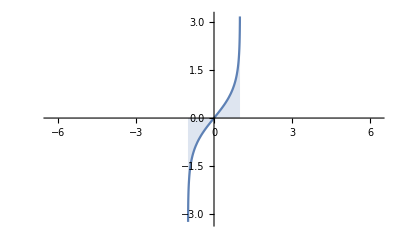

```mathematica
Plot[ArcTanh[x],{x,-2π,2π},Filling->Axis]
```

```mathematica
Sin[ArcTan[x]]/.{x->-5}
```

-5/(√26)

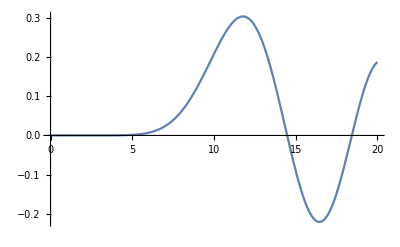

```mathematica
Plot[BesselJ[10,x],{x,0,20}]
```

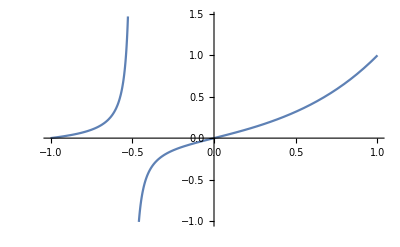

```mathematica
Plot[Gamma[2 z]/Gamma[z]^2,{z,-1,1}]
```

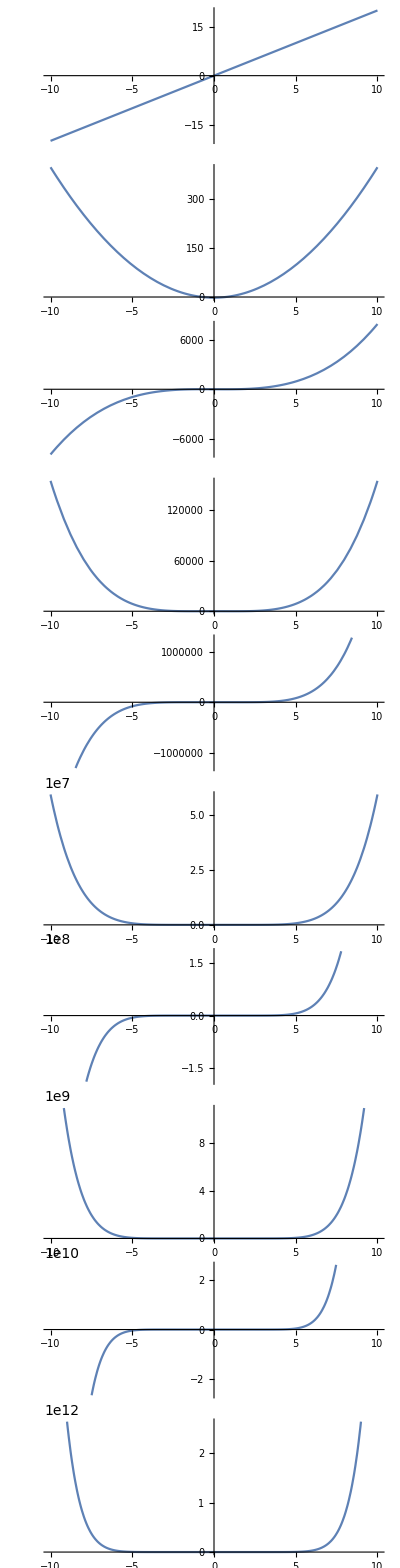

```mathematica
TableForm[Table[Plot[HermiteH[n,x],{x,-10,10}],{n,1,10}]]
```

```mathematica
?TableForm
```

```mathematica
N[Hypergeometric2F1[2,3,4,5]]
```

0.156542+0.150796 ⅈ

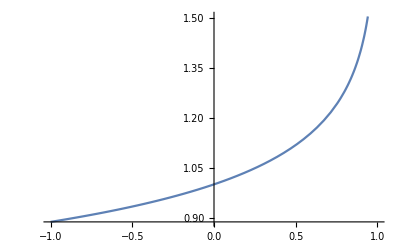

```mathematica
Plot[Hypergeometric2F1[1/3,1/3,2/3,x],{x,-1,1}]
```

```mathematica
ComplexPlot3D[Hypergeometric2F1[2,3,4,z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Series[Hypergeometric2F1[2,3,4,x],{x,0,5}]//Normal
```

1+(3 x)/2+(9 x^2)/5+2 x^3+(15 x^4)/7+(9 x^5)/4

```mathematica
Series[Hypergeometric2F1[2, 3, 4, x], {x, 1, 3}]
```

-3/(x-1)+3 (3+2 Log[1-x])-3 (5+6 Log[1-x]) (x-1)+3 (7+12 Log[1-x]) (x-1)^2-3 (9+20 Log[1-x]) (x-1)^3+O[x-1]^4

```mathematica
?Simplify
```

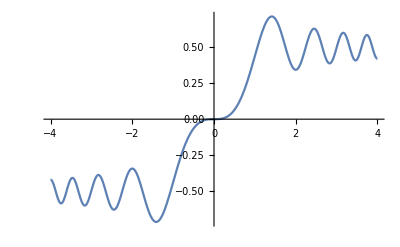

```mathematica
Plot[FresnelS[x],{x,-4,4}]
```

```mathematica
?*Mathieu*
```

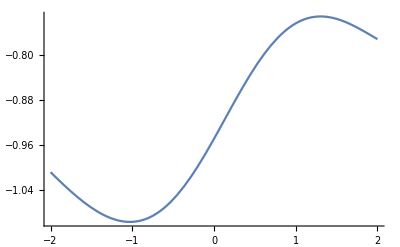

```mathematica
Plot[MathieuC[3,x,2],{x,-2,2}]
```

```mathematica
Clear[f];
f[x]=D[ArcSin[x],x]
```

1/(√(1-x^2))

```mathematica
Plot[f[x],{x,-1,1}]
```

-Graphics-

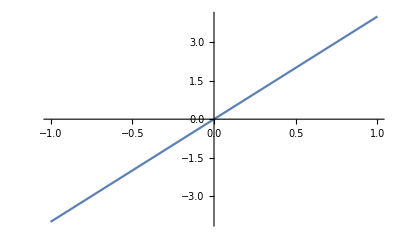

```mathematica
Plot[Evaluate[D[(2 x^2+3), x]],{x,-1,1}]
```

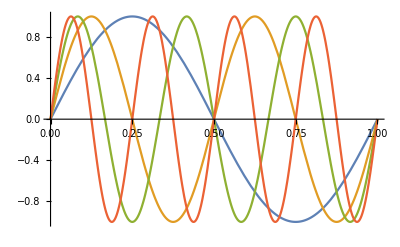

```mathematica
Plot[Evaluate[Table[Sin[2n π x],{n,1,4}]],{x,0,1}]
```

```mathematica
Clear[G]
```

```mathematica
G[Subscript[τ, 1],Subscript[τ, 2]]:=b Sign[Subscript[τ, 1]-Subscript[τ, 2]]/J^(2Δ)(f'[Subscript[τ, 1]]^Δ f'[Subscript[τ, 2]]^Δ)/(Abs[f[Subscript[τ, 1]]-f[Subscript[τ, 2]]])^(2Δ)
```

```mathematica
G[SubPlus[τ]+SubMinus[τ]/2,SubPlus[τ]-SubMinus[τ]/2]:=b Sign[SubMinus[τ]]/J^(2Δ)(f'[SubPlus[τ]+SubMinus[τ]/2]^Δ f'[SubPlus[τ]-SubMinus[τ]/2]^Δ)/(Abs[f[SubPlus[τ]+SubMinus[τ]/2]-f[SubPlus[τ]-SubMinus[τ]/2]])^(2Δ)
```

```mathematica
Series[G[SubPlus[τ]+SubMinus[τ]/2,SubPlus[τ]-SubMinus[τ]/2],{SubMinus[τ],0,2}]//Normal
```

Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) Sign[τ_-] (b J^(-2 Δ) f'[τ_+]^(2 Δ)+1/4 b J^(-2 Δ) Δ τ_-^2 f'[τ_+]^(-2+2 Δ) (-f''[τ_+]^2+f'[τ_+] f^(3)[τ_+]))

```mathematica
D[(G[SubPlus[τ]+SubMinus[τ]/2,SubPlus[τ]-SubMinus[τ]/2]), SubMinus[τ]]
```

-2 b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-1-2 Δ) Sign[τ_-] Abs'[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]] f'[-(τ_-)/2+τ_+]^Δ (1/2 f'[-(τ_-)/2+τ_+]+1/2 f'[(τ_-)/2+τ_+]) f'[(τ_-)/2+τ_+]^Δ+b J^(-2 Δ) Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) f'[-(τ_-)/2+τ_+]^Δ f'[(τ_-)/2+τ_+]^Δ Sign'[τ_-]-1/2 b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) Sign[τ_-] f'[-(τ_-)/2+τ_+]^(-1+Δ) f'[(τ_-)/2+τ_+]^Δ f''[-(τ_-)/2+τ_+]+1/2 b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) Sign[τ_-] f'[-(τ_-)/2+τ_+]^Δ f'[(τ_-)/2+τ_+]^(-1+Δ) f''[(τ_-)/2+τ_+]

```mathematica
D[(D[(G[SubPlus[τ]+SubMinus[τ]/2,SubPlus[τ]-SubMinus[τ]/2]), SubMinus[τ]]), SubMinus[τ]]
```

-2 b J^(-2 Δ) (-1-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2-2 Δ) Sign[τ_-] Abs'[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^2 f'[-(τ_-)/2+τ_+]^Δ (1/2 f'[-(τ_-)/2+τ_+]+1/2 f'[(τ_-)/2+τ_+])^2 f'[(τ_-)/2+τ_+]^Δ-4 b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-1-2 Δ) Abs'[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]] f'[-(τ_-)/2+τ_+]^Δ (1/2 f'[-(τ_-)/2+τ_+]+1/2 f'[(τ_-)/2+τ_+]) f'[(τ_-)/2+τ_+]^Δ Sign'[τ_-]-2 b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-1-2 Δ) Sign[τ_-] f'[-(τ_-)/2+τ_+]^Δ (1/2 f'[-(τ_-)/2+τ_+]+1/2 f'[(τ_-)/2+τ_+])^2 f'[(τ_-)/2+τ_+]^Δ Abs''[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]+2 b J^(-2 Δ) Δ^2 Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-1-2 Δ) Sign[τ_-] Abs'[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]] f'[-(τ_-)/2+τ_+]^(-1+Δ) (1/2 f'[-(τ_-)/2+τ_+]+1/2 f'[(τ_-)/2+τ_+]) f'[(τ_-)/2+τ_+]^Δ f''[-(τ_-)/2+τ_+]-b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) f'[-(τ_-)/2+τ_+]^(-1+Δ) f'[(τ_-)/2+τ_+]^Δ Sign'[τ_-] f''[-(τ_-)/2+τ_+]+1/4 b J^(-2 Δ) (-1+Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) Sign[τ_-] f'[-(τ_-)/2+τ_+]^(-2+Δ) f'[(τ_-)/2+τ_+]^Δ f''[-(τ_-)/2+τ_+]^2-2 b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-1-2 Δ) Sign[τ_-] Abs'[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]] f'[-(τ_-)/2+τ_+]^Δ f'[(τ_-)/2+τ_+]^Δ (-1/4 f''[-(τ_-)/2+τ_+]+1/4 f''[(τ_-)/2+τ_+])-2 b J^(-2 Δ) Δ^2 Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-1-2 Δ) Sign[τ_-] Abs'[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]] f'[-(τ_-)/2+τ_+]^Δ (1/2 f'[-(τ_-)/2+τ_+]+1/2 f'[(τ_-)/2+τ_+]) f'[(τ_-)/2+τ_+]^(-1+Δ) f''[(τ_-)/2+τ_+]+b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) f'[-(τ_-)/2+τ_+]^Δ f'[(τ_-)/2+τ_+]^(-1+Δ) Sign'[τ_-] f''[(τ_-)/2+τ_+]-1/2 b J^(-2 Δ) Δ^2 Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) Sign[τ_-] f'[-(τ_-)/2+τ_+]^(-1+Δ) f'[(τ_-)/2+τ_+]^(-1+Δ) f''[-(τ_-)/2+τ_+] f''[(τ_-)/2+τ_+]+1/4 b J^(-2 Δ) (-1+Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) Sign[τ_-] f'[-(τ_-)/2+τ_+]^Δ f'[(τ_-)/2+τ_+]^(-2+Δ) f''[(τ_-)/2+τ_+]^2+b J^(-2 Δ) Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) f'[-(τ_-)/2+τ_+]^Δ f'[(τ_-)/2+τ_+]^Δ Sign''[τ_-]+1/4 b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) Sign[τ_-] f'[-(τ_-)/2+τ_+]^(-1+Δ) f'[(τ_-)/2+τ_+]^Δ f^(3)[-(τ_-)/2+τ_+]+1/4 b J^(-2 Δ) Δ Abs[-f[-(τ_-)/2+τ_+]+f[(τ_-)/2+τ_+]]^(-2 Δ) Sign[τ_-] f'[-(τ_-)/2+τ_+]^Δ f'[(τ_-)/2+τ_+]^(-1+Δ) f^(3)[(τ_-)/2+τ_+]

```mathematica
Series[f[SubPlus[τ]+SubMinus[τ]/2],{SubMinus[τ],0,2}]
```

f[τ_+]+1/2 f'[τ_+] τ_-+1/8 f''[τ_+] τ_-^2+O[τ_-]^3

## Exercises